```mathematica
Exit[];
```

```mathematica
c={1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
```

{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}

```mathematica
b=1/n;
```

```mathematica
Y[i_,h_]:={y[i],y[i+1],m[i],m[i+1]}.c/.x->h;
{Y[i,0],Y[i,1/n],D[Y[i,x],x]/.x->0,D[Y[i,x],x]/.x->1/n}
```

{y[i],y[1+i],m[i],m[1+i]}

```mathematica
Simplify[(D[Y[1,x],{x,2}]/4 /n/.x->0)==0]
```

2 m[1]+m[2]+3 n y[1]==3 n y[2]

```mathematica
Simplify[(D[Y[n,x],{x,2}]/4 /n/.x->b)==0]
```

m[n]+2 m[1+n]+3 n y[n]==3 n y[1+n]

```mathematica
Simplify[(D[Y[i,x],{x,2}]/4 /n/.x->b)==(D[Y[i+1,x],{x,2}]/4 /n/.x->0)]
```

m[i]+4 m[1+i]+m[2+i]+3 n y[i]==3 n y[2+i]

```mathematica
M[n_]:=SparseArray[{{1,1}->-2,(n+1){1,1}->2,{n+1,n}->-2,{1,2}->2,{i_,j_}/;(i==j+1&&i<n+1&&i>1)->-1,{i_,j_}/;(i==j-1&&i<n+1&&i>1)->1},(n+1){1,1}];
M[5]//MatrixForm
```

(-2 | 2 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | -2 | 2)

# los:

```mathematica
y=Transpose[XY][[2]];n=Length[y]-1;m=M[n].y;
```

```mathematica
Y[x0_]:=Module[{i,x=x0,y=y,m=m,c=c,n=n},
i=Ceiling[x*n];
x-=(i-1)/n;
{y[[i]],y[[i+1]],m[[i]],m[[i+1]]}.{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
]
```

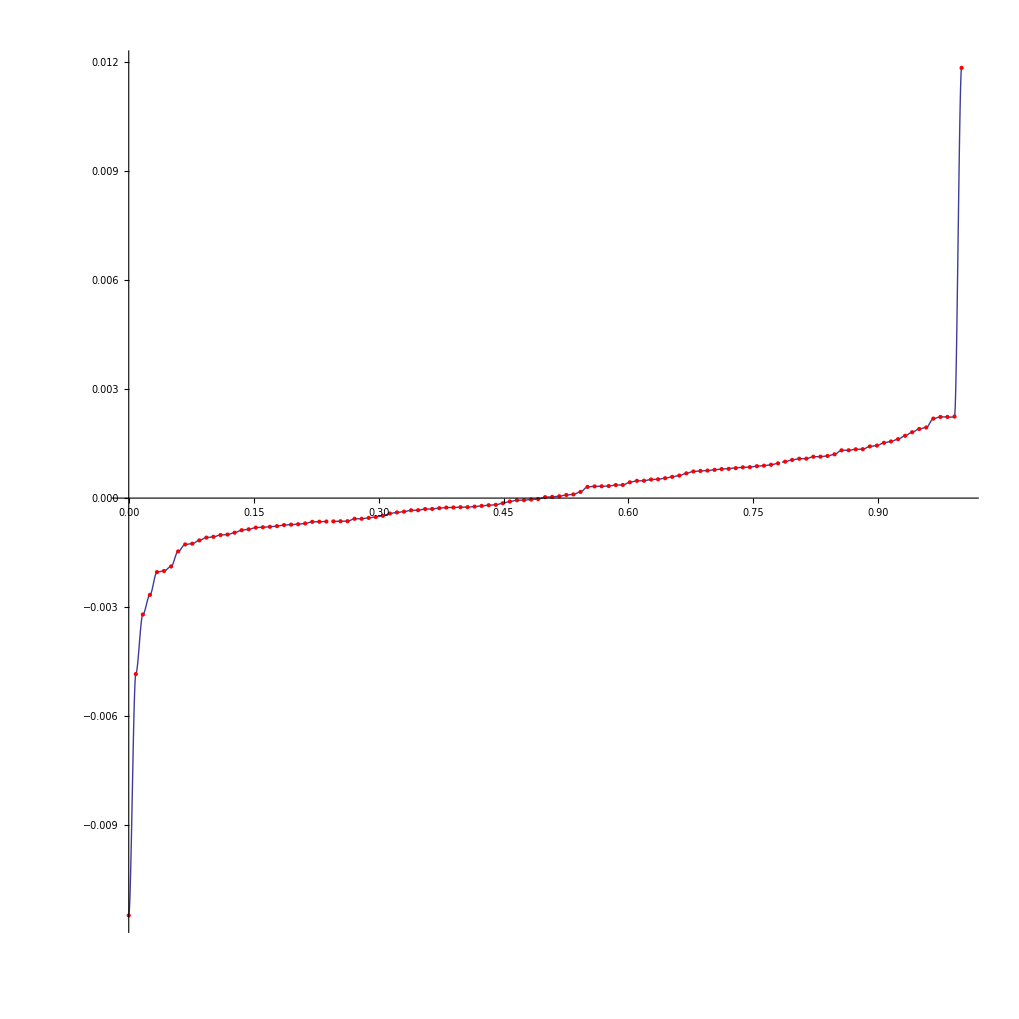

```mathematica
Show[Plot[Y[x],{x,0,1},AspectRatio->1,PlotRange->All],ListPlot[Table[{i/(Length[y]-1),y[[i+1]]},{i,0,Length[y]-1}],PlotStyle->Red]]
```

```mathematica
<<Splines`
```

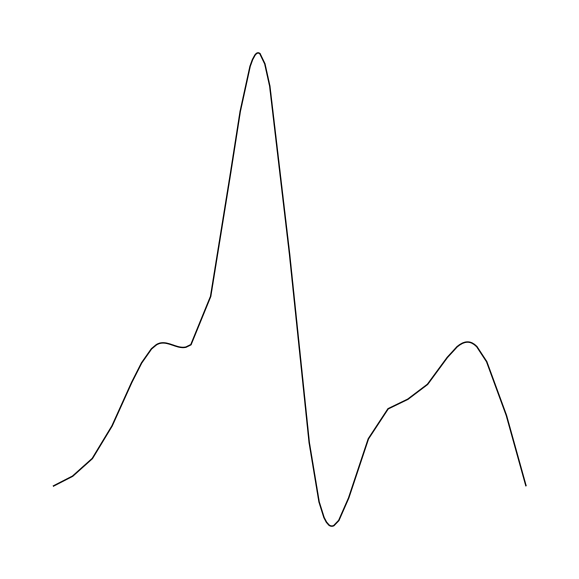

```mathematica
Graphics[Spline[Table[{i/(Length[y]-1),y[[i+1]]},{i,0,Length[y]-1}],Cubic],AspectRatio->1]
```

```mathematica
Y[x0_]:=Module[{a,delta,i=n,x=x0,p=P,m=m,kr=kr,n=n,b,y},
If[x0==0,i=1,
While[x≤p[[i,1]],i--];
];
b=p[[i+1,1]]-p[[i,1]];
{p[[i,2]],p[[i+1,2]],m[[i]],m[[i+1]]}.{1-3 n^2 x^2+2 n^3 x^3,3 n^2 x^2-2 n^3 x^3,x-2 n x^2+n^2 x^3,-n x^2+n^2 x^3}
]
```

```mathematica
n=8;nN=Length[XY];
P=Join[{1},Table[i,{i,Ceiling[(nN-(Floor[nN/n]-1)n)/2],nN,n}],{nN}];
n=Length[P]-1;
P=Table[{XY[[P[[i]],1]],XY[[P[[i]],2]]},{i,1,n+1}]
m=Table[ts[i],{i,n+1}];
```

{{0,-0.011473},{0.059322,-0.001466},{0.127119,-0.000951},{0.194915,-0.00073},{0.262712,-0.000635},{0.330508,-0.000373},{0.398305,-0.00025},{0.466102,-0.000059},{0.533898,0.000101},{0.601695,0.000434},{0.669492,0.00068},{0.737288,0.000846},{0.805085,0.001082},{0.872881,0.001341},{0.940678,0.001811},{1.,0.011826}}

```mathematica
d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}];g=Solve[Table[D[d,ts[i]]==0,{i,n+1}],m]
```

{{ts[1]→0.476741,ts[2]→-0.202484,ts[3]→0.0994919,ts[4]→-0.0576761,ts[5]→0.0442024,ts[6]→-0.0278467,ts[7]→0.0261955,ts[8]→-0.0170168,ts[9]→0.0192287,ts[10]→-0.00766155,ts[11]→0.0138237,ts[12]→-0.00780359,ts[13]→0.0138848,ts[14]→-0.00535186,ts[15]→0.0185076,ts[16]→0.272203}}

```mathematica
m=m=n/2M[n].Transpose[P][[2]];
For[i=1,i≤n,i++,
delta=(P[[i+1,2]]-P[[i,2]])/(P[[i+1,1]]-P[[i,1]]);
a=m[[i]]/delta;b=m[[i+1]]/delta;
If[a^2+b^2>3,
t=3/Sqrt[a^2+b^2];m[[i]]=t a delta;m[[i+1]]=t b delta;]
];m
```

{0.150105,0.0227331,0.00159015,0.00278623,0.00314773,0.0042178,0.00343997,0.00410635,0.0057676,0.0043425,0.00525751,0.00845994,0.00854837,0.00200951,0.0207001,0.150225}

```mathematica
d/.g[[1]]
```

0.0106315

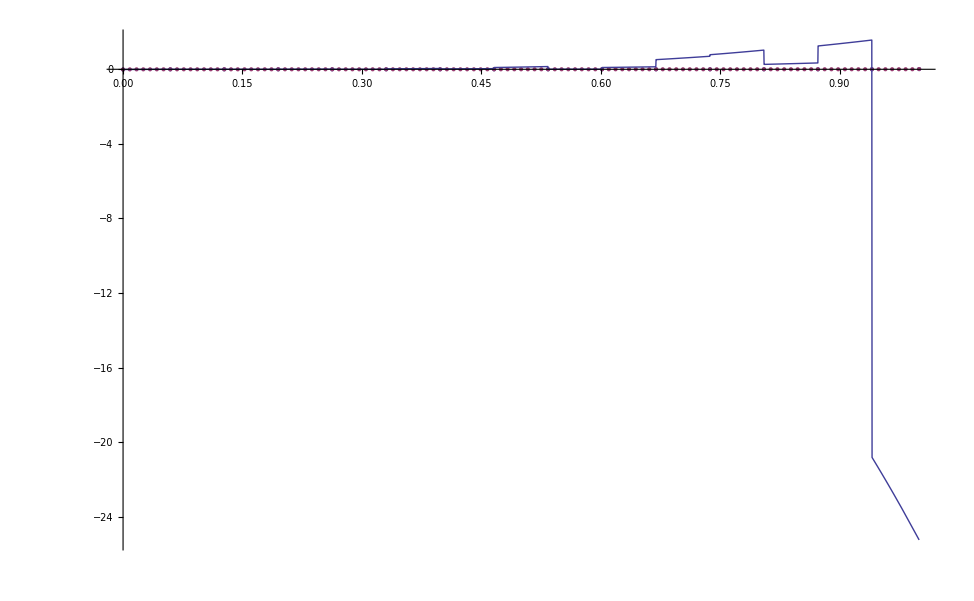

```mathematica
Show[ListPlot[{P,XY},PlotRange->All],Plot[Y[x]/.g[[1]],{x,0,1},PlotRange->All]]
```

```mathematica
Solve[Table[D[d,ys[i]]==0,{i,nN}],Table[ys[i],{i,nN}]]
```

{{ys[1]→-0.00547464,ys[2]→-0.000492335,ys[3]→-0.000911088,ys[4]→-0.00031071,ys[5]→-0.000185091,ys[6]→0.000265952,ys[7]→0.00060474,ys[8]→0.00113058,ys[9]→0.00100276,ys[10]→0.0046597}}

```mathematica
y=Table[ys[i],{i, nN}]/.%[[1]];
```

```mathematica
nN=10;y=Table[ys[i],{i, nN}];
```

0.000118941

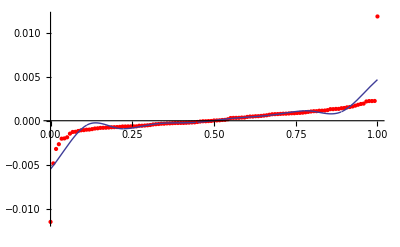

```mathematica
m=n/2M[n].y;n=Length[y]-1;d=(Y[#[[1]]]-#[[2]])^2&/@XY;d=Sum[d[[i]],{i,Length[d]}]
Show[ListPlot[XY,PlotStyle->Red,PlotRange->All],Plot[Y[x],{x,0,1},PlotRange->All]]
```

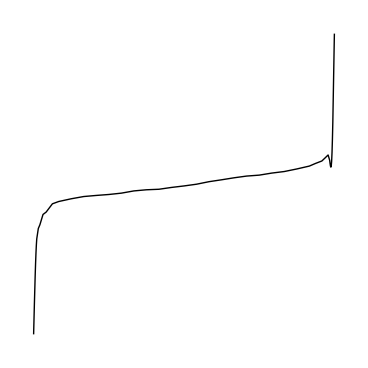

```mathematica
Graphics[Spline[XY,Cubic],AspectRatio->1]
```

```mathematica
Y[0]
```

0.01

```mathematica
{#[[1]]}&/@XY
```

{{0.},{0.008475},{0.016949},{0.025424},{0.033898},{0.042373},{0.050847},{0.059322},{0.067797},{0.076271},{0.084746},{0.09322},{0.101695},{0.110169},{0.118644},{0.127119},{0.135593},{0.144068},{0.152542},{0.161017},{0.169492},{0.177966},{0.186441},{0.194915},{0.20339},{0.211864},{0.220339},{0.228814},{0.237288},{0.245763},{0.254237},{0.262712},{0.271186},{0.279661},{0.288136},{0.29661},{0.305085},{0.313559},{0.322034},{0.330508},{0.338983},{0.347458},{0.355932},{0.364407},{0.372881},{0.381356},{0.389831},{0.398305},{0.40678},{0.415254},{0.423729},{0.432203},{0.440678},{0.449153},{0.457627},{0.466102},{0.474576},{0.483051},{0.491525},{0.5},{0.508475},{0.516949},{0.525424},{0.533898},{0.542373},{0.550847},{0.559322},{0.567797},{0.576271},{0.584746},{0.59322},{0.601695},{0.610169},{0.618644},{0.627119},{0.635593},{0.644068},{0.652542},{0.661017},{0.669492},{0.677966},{0.686441},{0.694915},{0.70339},{0.711864},{0.720339},{0.728814},{0.737288},{0.745763},{0.754237},{0.762712},{0.771186},{0.779661},{0.788136},{0.79661},{0.805085},{0.813559},{0.822034},{0.830508},{0.838983},{0.847458},{0.855932},{0.864407},{0.872881},{0.881356},{0.889831},{0.898305},{0.90678},{0.915254},{0.923729},{0.932203},{0.940678},{0.949153},{0.957627},{0.966102},{0.974576},{0.983051},{0.991525},{1.}}